{{vX[t]→22.5 ⅇ^(-0.235714 t),vY[t]→-41.6182 ⅇ^(-0.235714 t) (-1.9364 ⅇ^(2.77556×10^-17 t)+1. ⅇ^(0.235714 t))}}

22.5 ⅇ^(-0.235714 t)

95.4545-95.4545 ⅇ^(-0.235714 t)

341.894-341.894 ⅇ^(-0.235714 t)-51.4282 t

Solve::ifun: Solve 正在使用反函数，因此可能无法找到某些解；请使用 Reduce 来获取完整的解信息.

-4.24242 Log[0.0104761904761905 (95.4545454545455-1. x)]

341.894-3.58175 (95.4545454545455-1. x)^1.+218.18 Log[0.0104761904761905 (95.4545454545455-1. x)]

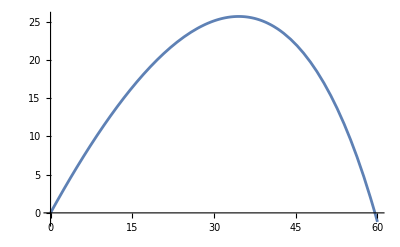

```mathematica
ClearAll["Global`*"]
m=0.14;  
v0=45;  
theta0=60 Degree;  
b=0.033;  
g=9.81;  

v0x=v0 Cos[theta0];
v0y=v0 Sin[theta0];

eqns={m D[vX[t],t]==-b vX[t],m D[vY[t],t]==-b vY[t]-m g,vX[0]==v0x,vY[0]==v0y  };


solutions1=DSolve[eqns,{vX[t],vY[t]},t];
solutions1

vxSol[t_]=vX[t]/. solutions1[[1]];
vySol[t_]=vY[t]/. solutions1[[1]];
vxSol[t]
(*积分得xy*)
xSol[t_]=Integrate[vxSol[t],{t,0,t}];
xSol[t]
ySol[t_]=Integrate[vySol[t],{t,0,t}]-m g t/m;
ySol[t]


(*反解t(x)*)
tSol=Solve[xSol[t]==x,t][[1,1,2]];
tSol

(*带入y得到y(x)*)
yFunc=ySol[tSol];

(*轨道方程*)
yFunc

Plot[yFunc,{x,0,60}]
```

General::prng: 选项值 PlotRange -> {{0,95.4545-95.4545 ⅇ^(-0.235714 t)},{0,20}} 不是 All、Full、Automatic、一个机器精度正数，或者由范围指定组成的恰当列表.

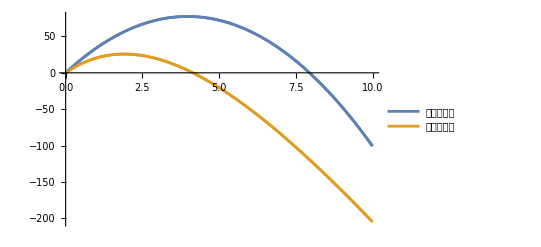

```mathematica
(*无空气阻力*)
x0[t_]=v0x t;
y0[t_]=v0y t-1/2 g t^2;

Show[Plot[{y0[t],ySol[t]},{t,0,10},PlotRange->{{0,Max[xSol[t]]},{0,20}},PlotLegends->{"无空气阻力","有空气阻力"}],Plot[{y0[t],ySol[t]},{t,0,10}]]
```